```mathematica
(*Mathematica*)
```

```mathematica
(* quartic Cauchy distribution function*)
```

```mathematica
f[x_]=1/(1+x^4)
```

1/(1+x^4)

```mathematica
Plot[f[x],{x,-10,10},PlotRange->All]
```

```mathematica
Integrate[1/(1+x^4),{x,-Infinity,Infinity}]
```

π/(√2)

```mathematica
(*Conjugate polynomials*)
```

```mathematica
p[x_]=-x+I
q[x_]=-x-I
```

ⅈ-x

-ⅈ-x

```mathematica
ExpandAll[p[x]*q[x]]
```

1+x^2

```mathematica
(*Integration constant*)
```

```mathematica
c=1/(√2*π)
```

1/(√2 π)

```mathematica
Integrate[c*(p[x]*q[x])/(1+x^4),{x,-Infinity,Infinity}]
```

1

```mathematica
p[x]*Sqrt[f[x]]
```

(ⅈ-x) √(1/(1+x^4))

```mathematica
ComplexPlot[p[x]*Sqrt[f[x]],{x,-3-I*3,3+I*3},PlotRange->All,ColorFunction->"CyclicReImLogAbs",ImageSize->Full]
```

```mathematica
ComplexPlot[q[x]*Sqrt[f[x]],{x,-3-I*3,3+I*3},PlotRange->All,ColorFunction->"CyclicReImLogAbs",ImageSize->Full]
```

```mathematica
ComplexPlot[p[x]*q[x]*f[x],{x,-3-I*3,3+I*3},PlotRange->All,ColorFunction->"CyclicReImLogAbs",ImageSize->Full]
```

```mathematica
(*Quartic Cauchy Orthongonal polynomial "Hat" distribution*)
```

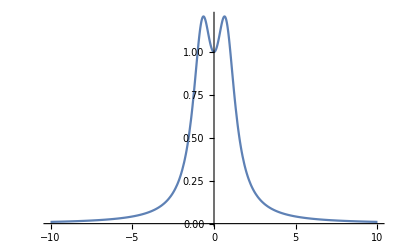

```mathematica
Plot[p[x]*q[x]*f[x],{x,-10,10},PlotRange->All]
```

```mathematica
(*quartic roots)
```

```mathematica
r[i_]:=x/.Solve[1+x^4==0,x][[i]]
```

```mathematica
pr[x_,i_]:=-x-r[i]
```

```mathematica
(* quartic factor polynomials :root group*)
```

```mathematica
Table[pr[x,i],{i,4}]
```

{(-1)^(1/4)-x,-(-1)^(1/4)-x,(-1)^(3/4)-x,-(-1)^(3/4)-x}

```mathematica
(* root matrix inverses*)
```

```mathematica
s[1]={{0,1},{-1,(-1)^(1/4)}}
s[2]={{0,1},{-1,-(-1)^(1/4)}}
s[3]={{0,1},{-1,(-1)^(3/4)}}
s[4]={{0,1},{-1,-(-1)^(3/4)}}
```

```mathematica
(*Molien function*)
```

```mathematica
ExpandAll[Together[Sum[1/pr[x,i],{i,4}]]]
```

-(4 x^3)/(1+x^4)

```mathematica
(* anti-diagonal orthogonality matrix*)
```

```mathematica
TableForm[Table[Integrate[c*(pr[x,i]*pr[x,j])/(1+x^4),{x,-Infinity,Infinity}],{i,4},{j,4}]]
```

1/2+ⅈ/2 | 1/2-ⅈ/2 | 0 | 1
1/2-ⅈ/2 | 1/2+ⅈ/2 | 1 | 0
0 | 1 | 1/2-ⅈ/2 | 1/2+ⅈ/2
1 | 0 | 1/2+ⅈ/2 | 1/2-ⅈ/2

```mathematica
ExpandAll[pr[x,1]*pr[x,2]]
```

-ⅈ+x^2

```mathematica
ExpandAll[pr[x,3]*pr[x,4]]
```

ⅈ+x^2

```mathematica
TableForm[Table[ExpandAll[(pr[x,i]*pr[x,j])/(1+x^4)],{i,4},{j,4}]]
```

ⅈ/(1+x^4)-(2 (-1)^(1/4) x)/(1+x^4)+x^2/(1+x^4) | -ⅈ/(1+x^4)+x^2/(1+x^4) | -1/(1+x^4)-((-1)^(1/4) x)/(1+x^4)-((-1)^(3/4) x)/(1+x^4)+x^2/(1+x^4) | 1/(1+x^4)-((-1)^(1/4) x)/(1+x^4)+((-1)^(3/4) x)/(1+x^4)+x^2/(1+x^4)
-ⅈ/(1+x^4)+x^2/(1+x^4) | ⅈ/(1+x^4)+(2 (-1)^(1/4) x)/(1+x^4)+x^2/(1+x^4) | 1/(1+x^4)+((-1)^(1/4) x)/(1+x^4)-((-1)^(3/4) x)/(1+x^4)+x^2/(1+x^4) | -1/(1+x^4)+((-1)^(1/4) x)/(1+x^4)+((-1)^(3/4) x)/(1+x^4)+x^2/(1+x^4)
-1/(1+x^4)-((-1)^(1/4) x)/(1+x^4)-((-1)^(3/4) x)/(1+x^4)+x^2/(1+x^4) | 1/(1+x^4)+((-1)^(1/4) x)/(1+x^4)-((-1)^(3/4) x)/(1+x^4)+x^2/(1+x^4) | -ⅈ/(1+x^4)-(2 (-1)^(3/4) x)/(1+x^4)+x^2/(1+x^4) | ⅈ/(1+x^4)+x^2/(1+x^4)
1/(1+x^4)-((-1)^(1/4) x)/(1+x^4)+((-1)^(3/4) x)/(1+x^4)+x^2/(1+x^4) | -1/(1+x^4)+((-1)^(1/4) x)/(1+x^4)+((-1)^(3/4) x)/(1+x^4)+x^2/(1+x^4) | ⅈ/(1+x^4)+x^2/(1+x^4) | -ⅈ/(1+x^4)+(2 (-1)^(3/4) x)/(1+x^4)+x^2/(1+x^4)

```mathematica
Table[ComplexPlot[ExpandAll[(pr[x,i]*pr[x,j])/(1+x^4)],{x,-3-I*3,3+I*3},PlotRange->All,ColorFunction->"CyclicReImLogAbs",ImageSize->Full],{i,4},{j,4}]
```

```mathematica
(*end*)
```

```mathematica
(* Mathematica*)
Clear[cr,cols,cr2,cr3,cr4,p,p0,q0,r0,s0,s,v]
allColors=ColorData["Legacy"][[3,1]];
firstCols={ "Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+8]];
cr3[n_]:=cr3[n]=cols[[n+16]];
cr4[n_]:=cr4[n]=cols[[n+24]];
cr5[n_]:=cr5[n]=cols[[n+36]]
```

```mathematica
(*quartic roots*)
```

```mathematica
r[i_]:=x/.Solve[1+x^4==0,x][[i]]
```

```mathematica
pr[x_,i_]:=-x-r[i]
```

```mathematica
(* quartic factor polynomials :root group*)
```

```mathematica
Table[pr[x,i],{i,4}]
```

{(-1)^(1/4)-x,-(-1)^(1/4)-x,(-1)^(3/4)-x,-(-1)^(3/4)-x}

```mathematica
sc=2.0
```

2.

```mathematica
(* root matrix inverses*)
```

```mathematica
s[1]={{0,1},{-1,(-1)^(1/4)*sc}}
s[2]={{0,1},{-1,-(-1)^(1/4)*sc}}
s[3]={{0,1},{-1,(-1)^(3/4)*sc}}
s[4]={{0,1},{-1,-(-1)^(3/4)*sc}}
```

{{0,1},{-1,1.41421+1.41421 ⅈ}}

{{0,1},{-1,-1.41421-1.41421 ⅈ}}

{{0,1},{-1,-1.41421+1.41421 ⅈ}}

{{0,1},{-1,1.41421-1.41421 ⅈ}}

```mathematica
(*Molien function*)
```

```mathematica
ExpandAll[Together[Sum[1/pr[x,i],{i,4}]]]
```

-(4 x^3)/(1+x^4)

```mathematica
s[5]=N[{{1+I,1},{1,1-I}}]
s[6]=Inverse[s[5]]
s[7]={{1,0},{0,1}}
s[8]={{1,0},{0,1}}
```

{{1.+1. ⅈ,1.},{1.,1.-1. ⅈ}}

{{1.-1. ⅈ,-1.+0. ⅈ},{-1.+0. ⅈ,1.+1. ⅈ}}

{{1,0},{0,1}}

{{1,0},{0,1}}

```mathematica
Table[Det[s[i]],{i,8}]//Chop

Table[Tr[s[i]],{i,8}]//Chop
Sum[s[i].s[i],{i,8}]//Chop
```

{1.,1.,1.,1.,1.,1.,1,1}

{1.41421+1.41421 ⅈ,-1.41421-1.41421 ⅈ,-1.41421+1.41421 ⅈ,1.41421-1.41421 ⅈ,2.,2.,2,2}

{{0,0},{0,0}}

```mathematica
(* the Möbius transforms : Kleinian group in SL(2,c)*)
```

```mathematica
s0=N[{{1,-I},{-I,1}}/Sqrt[2]];s1=Inverse[s0];
qf=N[rotate[Pi/4]];qfi=Inverse[qf];
{a,b,c,d,A0,B0,C0,D0}=Table[N[s[i]],{i,8}]
```

{{{0.,1.},{-1.,1.41421+1.41421 ⅈ}},{{0.,1.},{-1.,-1.41421-1.41421 ⅈ}},{{0.,1.},{-1.,-1.41421+1.41421 ⅈ}},{{0.,1.},{-1.,1.41421-1.41421 ⅈ}},{{1.+1. ⅈ,1.},{1.,1.-1. ⅈ}},{{1.-1. ⅈ,-1.+0. ⅈ},{-1.+0. ⅈ,1.+1. ⅈ}},{{1.,0.},{0.,1.}},{{1.,0.},{0.,1.}}}

```mathematica
Det[a]
Tr[a]
Det[b]
Tr[b]
Det[A0]
Tr[A0]
Det[B0]
Tr[B0]
```

1.+0. ⅈ

1.41421+1.41421 ⅈ

1.+0. ⅈ

-1.41421-1.41421 ⅈ

1.+0. ⅈ

2.+0. ⅈ

1.+0. ⅈ

2.+0. ⅈ

```mathematica
Affine[{z1_,z2_}]:=0.00001 Round[(z1/z2)/0.00001];
Children[{z_,n_}]:={Affine[{a,b,c,d,A0,B0,C0,D0}[[#]].{z,1}],#}&/@Delete[Range[8],{5,6,7,8,1,2,3,4}[[n]]];
aa1={Re[#[[1]]],Im[#[[1]]]}&/@Nest[Union[Flatten[Children/@#,1]]&,ParallelTable[{Affine[{a,b,c,d,A0,B0,C0,D0}[[i]].{0,1}],i},{i,1,8}],7];
ll=Length[aa1]
Last[aa1]
aa=Delete[Reverse[Union[aa1]],1];
```

1046891

{0.90882,0.35369}

```mathematica
g0=ListPlot[aa,AspectRatio->Automatic,ColorFunction->Hue,PlotStyle->{PointSize[0.001]},ImageSize->2000,PlotRange->{{-1.1,1.1},{-1.1,1.1}},Axes->False];
```

```mathematica
dlst=ParallelTable[Mod[1+Floor[1+(1+Floor[48*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst];
Max[dlst];
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g2=Rasterize[Graphics[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,PlotRange->{{-1.05,1.05},{-1.05,1.05}},Background->Black],RasterSize->2000,ImageSize->2000];
```

```mathematica
(* end limit set*)
Export["Nylander_5group_Quartic_roots_on_Disk_8Limit_7.jpg",{g0,g2}]
```

Nylander_5group_Quartic_roots_on_Disk_8Limit_7.jpg